# Parcialne diferencialne enačbe (1. del)

## Enačba valovanja (nihanja)

(∂^2 u)/(∂ t^2)=a^2 Δ u

1. korak: Separacija spremenljivk
2. korak: Iščemo rešitve, ki ustrezajo robnim pogojem
3. korak: Zadostimo še začetnim pogojem

### Lastna nihanja vpete strune

u_tt=a^2 u_xx             0<x<L, t>0

               u(0,t)=u(L,t)=0    Homogeni robni pogoji.  k=negativen

1. korak: Separacija spremenljivk

u[x,t]=F[x]G[t]
G''[t]/(a^2 G[t])=F''[x]/F[x]=-k^2(homogeni robni pogoji, vemo da samo v primeru negativne konstante dobimo netrivialne rešitve)

F''[x]+k^2 F[x]=0
G''[t]+a^2 k^2 G[t]=0

2. korak: Rešitve, ki ustrezajo robnim pogojem

F[x]=A Cos[k x]+B Sin[k x]
F[0]=0  ...sledi...   A=0
F[L]=0   ...sledi...   Sin[k L]=0   ...sledi...   k=(n π)/L , n=1,2,3...
F_n[x]=Sin[(n π x)/L]
λ_n=(n π a)/L
G_n[t]=C_n Cos[λ_n t]+D_n Sin[λ_n t]

u_n[x,t]=(C_n Cos[λ_n t]+D_n Sin[λ_n t])Sin[(n π x)/L]

Lastna nihanja strune: λ_n=(n π a)/L, n = 1, 2, 3 ...

```mathematica
L=1;
a=1;
n=7;
Subscript[λ, n]=(n π a)/L;
Subscript[u, n][x_,t_]:=Sin[Subscript[λ, n] t]Sin[(n π x)/L];
Animate[
Plot[Subscript[u, n][x,t],{x,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-1,1}}],
{t,0,(2L)/a,(2L)/(100 a)}]
```

### Prosto nihanje prožne (vpete) strune

u_tt=a^2 u_xx            0<x<L, t>0

               u(0,t)=u(L,t)=0    HOMOGENI ROBNI POGOJI
               u(x,0)=f_1(x)   Začetna oblika strune. 

u_t(x,0)=f_2(x)  Začetna hitrost.

3. korak: Zadostiti želimo še začetnim pogojem

u[x,t]=(∑_^)_(n=1)^∞(C_n Cos[λ_n t]+D_n Sin[λ_n t])Sin[(n π x)/L]

za t = 0 sledi ...

f1[x]=(∑_^)_(n=1)^∞C_n Sin[(n π x)/L]  ...sledi...
C_n je koeficient v sinusni Fourierovi vrsti za f1[x] na intervalu (0,L)

f2[x]=(∑_^)_(n=1)^∞D_n λ_n Sin[(n π x)/L]  ...sledi...
D_n λ_n je koeficient v sinusni Fourierovi vrsti za f2[x] na intervalu (0,L)

Podatki

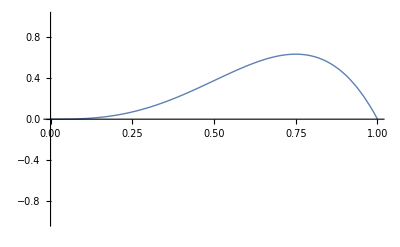

```mathematica
L=1;
a=1;
Zacet={
Piecewise[{{x/L,x<L/2},{(L-x)/L,x>L/2}}],
Piecewise[{{(2x)/L,x<L/4},{L/2,L/4<x<(3L)/4},{(2(L-x))/L,x>(3L)/4}}],
6x^3(L-x)
};(*Seznam nekaj začetnih odmikov, katerega vzamem0*)
f1[x_]=Zacet[[3]];

Plot[f1[x],{x,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-1,1}}]
f2[x_]:=0;
(*Začetna hitrosj je 0. sTRUNO PO ODMIKU PROSTO SPUSTIMO*)
```

Rešitev

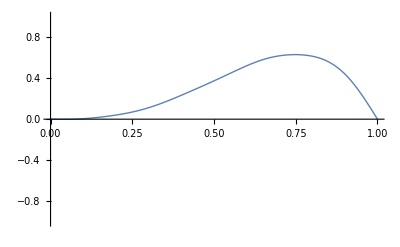

```mathematica
M=8; (* število členov v vrsti *)
λ=Table[(n π a)/L,{n,1,M}];
c=Table[2/L Integrate[f1[x]Sin[(n π x)/L],{x,0,L}],{n,1,M}];(*Izračun Cn koeficienta v sinusni F vrsti*)
d=Table[2/(L λ_⟦n⟧)Integrate[f2[x]Sin[(n π x)/L],{x,0,L}],{n,1,M}];(*Dn v sinusni F vrsti za začetno hitrost*)
u[x_,t_]:=Sum[(c_⟦n⟧Cos[ λ_⟦n⟧t]+d_⟦n⟧Sin[ λ_⟦n⟧t])Sin[(n π x)/L],{n,1,M}]
(* Preizkus začetne vrednosti: *)
Plot[u[x,0],{x,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-1,1}}]
```

```mathematica
Animate[
Plot[u[x,t],{x,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-1,1}}],
{t,0,(2L)/a,(2L)/(100 a)}]
```

### Primeri nalog za preverjanje

1. Poiščite rešitev u(x,y) parcialne diferencialne enačbe
               u_x+y u =y^2,
               u(0,y)=y+3.
      Koliko je u(1,2)?

Rezultat: 2.40601

```mathematica
(*ker imamo parcialne le po x lahko rečemo da je u odvisen le od x -> dobimo navadno de*)
DSolve[{u'[x]+y u[x]== y^2,u[0]==y+3}, u[x],x] //Flatten
%/.x-> 1 /.y-> 2 //N 
u[x]/.%%/.x-> 1 /.y-> 2 //N
```

{u[x]→ⅇ^(-x y) (3+ⅇ^(x y) y)}

{u[1.]→2.40601}

2.40601

```mathematica
(*ali*)
Clear[x,y,u]
DSolve[{D[u[x,y],x] + y u[x,y]==y^2, u[0,y]== y +3},u[x,y],{x,y}]//Flatten
u[x,y]/.%/.x-> 1 /.y-> 2 //N
```

{u[x,y]→ⅇ^(-x y) (3+ⅇ^(x y) y)}

2.40601

2. Poiščite rešitev u(x,y) parcialne diferencialne enačbe
               u_(x y)+y u_x =x y,
               u(0,y)=y+1,
               u_x(x,0)=2x+1.
      Koliko je u(1,2)?

Rezultat: 3.703

```mathematica
(*naredimo substitucijo v= u_x, da nam pridejo le odvodi po eni spremenljivki - le po x... dalje si mislimo da je v odvisen le od y *)
Clear[v,y,x]
DSolve[{v'[y]+y v[y]==x y, v[0]==2 x+1}, v[y],y]//Flatten
(*Rešujemo u_x je enako temu dobljenemu v-ju... spet imamo parcialne odvode le po eni sremenljivku - tokrat po x ... mislimo si, da je u odvisen el od x*)
DSolve[{u'[x]== (v[y]/.%), u[0]==y+1},u[x],x]//Flatten
u[x]/.%/. {x-> 1,y-> 2}//N
```

{v[y]→ⅇ^(-y^2/2) (1+x+ⅇ^(y^2/2) x)}

{u[x]→1/2 ⅇ^(-y^2/2) (2 ⅇ^(y^2/2)+2 x+x^2+ⅇ^(y^2/2) x^2+2 ⅇ^(y^2/2) y)}

3.703

3. Poiščite rešitev u(x,y) parcialne diferencialne enačbe
               u_x+x u_y =0,
               u(1,1)=1,
               u(1,2)=2,
      v obliki u(x,y)=X(x)Y(y). Koliko je u(2,1)?

Rezultat: 0.353553

```mathematica
Clear[x,y,u,c,U]
u=X[x]  Y[y]
D[u,x]/(x u)==- x D[u,y]/(x u)==k

DSolve[X'[x]/(x X[x])==k, X[x],x]//Flatten (*Rešitev za x*)
DSolve[-Y'[y]/Y[y]==k,Y[y],y]//Flatten (*Rešitev za y*)
U[x_,y_]=u/. %/.%%/. C[1]^2-> c
Solve[{U[1,1]==1,U[1,2]==2}, {c,k}, Reals]//Flatten

U[2,1]/.%//N

(*Če ne pa si označi*)
```

X[x] Y[y]

X'[x]/(x X[x])==-Y'[y]/Y[y]==k

{X[x]→ⅇ^((k x^2)/2) C[1]}

{Y[y]→ⅇ^(-k y) C[1]}

c ⅇ^((k x^2)/2-k y)

{c→1/(√2),k→-Log[2]}

0.353553

4. Poiščite rešitev u(x,t) parcialne diferencialne enačbe
               u_xx=1/c^2 u_tt,
               u(0,t)=u(L,t)=0,
               u(x,0)=x(L-x),
               u_t(x,0)=0,
      kjer je c=1.5 in L=3. Vzemite prvih pet členov Fourierove vrste (to pomeni do vključno A_5).
      Koliko je u(1,2)?

Rezultat: -1.99492

```mathematica
Clear[n,k,x,y,u,c,U,L,A,B]
(*Separacija*)
u=F[x] G[t]
D[u,x,x]/u==1/c^2 D[u,t,t]/u == -k^2(*homogeni robni pogoji*)



rF= DSolve[{F''[x]/F[x]==-k^2, F[0]==0}, F[x], x]/.C[2]-> 1// Flatten
Solve[(F[x]/.rF/. x-> L)==0,k]
k=n Pi/L




rG=DSolve[G''[t]/(c^2 G[t])==-k^2, G[t], t]/. {C[1]-> A[n], C[2]-> B[n]}//Flatten


(*Zaetni pogoji*)
U[x_,t_]=Sum[u/.rF/.rG,{n,1,Infinity}]
U[x,0]==x(L-x)
(*Dobili smo sinusno FV*)
A[n_]=2/L Integrate[x (L-x) Sin[n Pi x/L],{x,0,L}]

(*Drugi pogoj*)
(D[U[x,t],t]/. t-> 0)==0
B[n_]=0

(*Rešitev*)
c=1.5
L=3
U[x_,t_]=Sum[u/.rF/.rG,{n,1,5}](*Nloga zahteva le 5 členov*)
U[1,2]//N
```

F[x] G[t]

F''[x]/F[x]==G''[t]/(c^2 G[t])==-k^2

{F[x]→Sin[k x]}

{{L→ConditionalExpression[(2 π C[1])/k,C[1]∈ℤ]},{L→ConditionalExpression[(π+2 π C[1])/k,C[1]∈ℤ]}}

(n π)/L

{G[t]→A[n] Cos[(c n π t)/L]+B[n] Sin[(c n π t)/L]}

∑_(n=1)^∞ (A[n] Cos[(c n π t)/L]+B[n] Sin[(c n π t)/L]) Sin[(n π x)/L]

∑_(n=1)^∞ A[n] Sin[(n π x)/L]==(L-x) x

-(2 L^2 (-2+2 Cos[n π]+n π Sin[n π]))/(n^3 π^3)

∑_(n=1)^∞ (c n π B[n] Sin[(n π x)/L])/L==0

0

1.5

3

(72 Cos[1.5708 t] Sin[(π x)/3])/π^3+(8 Cos[4.71239 t] Sin[π x])/(3 π^3)+(72 Cos[7.85398 t] Sin[(5 π x)/3])/(125 π^3)

-1.99492

5. Poiščite rešitev u(x,t) parcialne diferencialne enačbe
               u_xx=1/c^2 u_t,
               u(0,t)=u(L,t)=0,
               u(x,0)=x(L-x),
      kjer je c=1/4 in L=2. Vzemite prvih pet členov Fourierove vrste (to pomeni do vključno A_5).
      Koliko je u(1,2)?

Rezultat: 0.755769

```mathematica
Clear[n,k,x,y,u,c,U,L,A,B]
(*Separacija*)
u=F[x] G[t]
D[u,x,x]/u==1/c^2 D[u,t]/u == -k^2(*homogeni robni pogoji TUKAJ IMAMO LE PRVI ODVOD*)



rF= DSolve[{F''[x]/F[x]==-k^2, F[0]==0}, F[x], x]/.C[2]-> 1// Flatten
Solve[(F[x]/.rF/. x-> L)==0,k]
k=n Pi/L




rG=DSolve[G'[t]/(c^2 G[t])==-k^2, G[t], t]/. {C[1]-> A[n], C[1]-> B[n]}//Flatten
(*TUKAJ NIMAMO C[2]*)

(*Zaetni pogoji*)
U[x_,t_]=Sum[u/.rF/.rG,{n,1,Infinity}]
U[x,0]==x(L-x)
(*Dobili smo sinusno FV*)
A[n_]=2/L Integrate[x (L-x) Sin[n Pi x/L],{x,0,L}]

(*TEGA DELA NIMAMO, NI BILO DRUGEGA ODVODA. Drugi pogoj
(D[U[x,t],t]/. t-> 0)==0
B[n_]=0
*)
(*RešitevPOPRAVIMO VREDNOSTI ZA C IN L*)
c=1/4
L=2
U[x_,t_]=Sum[u/.rF/.rG,{n,1,5}](*Nloga zahteva le 5 členov*)
U[1,2]//N
```

F[x] G[t]

F''[x]/F[x]==G'[t]/(c^2 G[t])==-k^2

{F[x]→Sin[k x]}

{{k→ConditionalExpression[(2 π C[1])/L,C[1]∈ℤ]},{k→ConditionalExpression[(π+2 π C[1])/L,C[1]∈ℤ]}}

(n π)/L

{G[t]→ⅇ^(-(c^2 n^2 π^2 t)/L^2) A[n]}

∑_(n=1)^∞ ⅇ^(-(c^2 n^2 π^2 t)/L^2) A[n] Sin[(n π x)/L]

∑_(n=1)^∞ A[n] Sin[(n π x)/L]==(L-x) x

-(2 L^2 (-2+2 Cos[n π]+n π Sin[n π]))/(n^3 π^3)

1/4

2

(32 ⅇ^(-(π^2 t)/64) Sin[(π x)/2])/π^3+(32 ⅇ^(-(9 π^2 t)/64) Sin[(3 π x)/2])/(27 π^3)+(32 ⅇ^(-(25 π^2 t)/64) Sin[(5 π x)/2])/(125 π^3)

0.755769